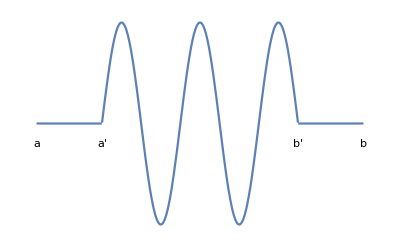

```mathematica
(* FUNCION TEST *)
a = -0.2;
test = Plot[Piecewise[{{0,x<0.2},{0,x>0.8},{Sin[(x-0.2)*(5*Pi/0.6)],x≥0.1 &&x≤0.9}}],{x,0,1}, Axes->False];
labels = {Graphics[Text["a",{0,a}]], Graphics[Text["a'",{0.2,a}]], Graphics[Text["b'",{0.8,a}]], Graphics[Text["b",{1,a}]]};
Show[test,labels]
```

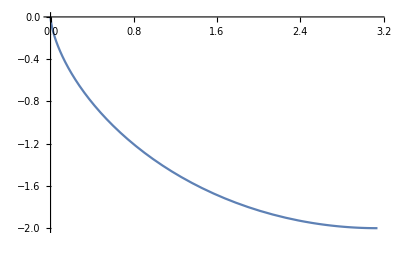

```mathematica
(* CICLOIDE *)
ParametricPlot[{u-Sin[u],Cos[u]-1},{u,0,Pi}]
```

```mathematica
(* ESCALERA DE CANTOR *)
puntos={{-.5,0},{0,0},{1/3,1/2},{2/3,1/2},{1,1},{1.5,1}};
n2 = ListPlot[{{0,0},{1/9,1/4},{2/9,1/4},{1/3,1/2}},PlotJoined->True, PlotStyle->Red,PlotLabel->"n=2"];
n3 = ListPlot[{{2/3,0.5},{1/9+2/3,1/4+0.5},{2/9+2/3,1/4+0.5},{1/3+2/3,1/2+0.5}},PlotJoined->True, PlotStyle->Red];
Show[ListPlot[puntos,PlotJoined->True],ListPlot[{Labeled[{2/3,0.5},"2/3"],Labeled[{1/3,0.5},"1/3"]}],n2,n3]
```

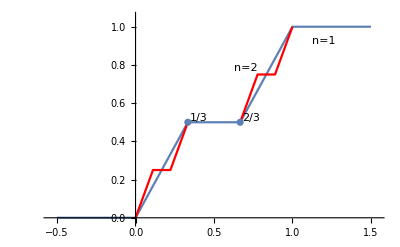
```mathematica
-Graphics-

Show[ListPlot[{{0,0},{1/3,0},{2/3,1},{1,1}},PlotJoined->True],ListPlot[{{1/3,0},{1/3+1/9,1/2},{1/3+2/9,1/2},{2/3,1}},PlotJoined->True, PlotStyle->Red]]
```

-Graphics-